## Catch

Define constant and physics rules.

```mathematica
conRules = {
	xcatch->3, (* m, catch height *)
	x10 -> 5, (* m, height of puck passing break beam *)
	x20 -> 4, (* m, height of platform when break beam tripped *)
	xf -> 2.5, (* m, final height *)
	tf -> 3, (* s, time when platform/puck at final height *)
	v10 -> -1, (* m/s, velocity of puck passing break beam *)
	v20 -> 0,  (* m/s, velocity of platform when puck passing break beam *)
	g -> -9.81 (* m/s^2 *)
};
physicsRules = {
	v1[t] -> (a1[t]//Integrate[#,t]+v10&),
	v2[t] -> (a2[t]//Integrate[#,t]+v20&),
	x1[t] -> (v1[t]//Integrate[#,t]+x10&),
	x2[t] -> (v2[t]//Integrate[#,t] + x20&)
};
a1[t_]:= g;
a2[t_]:=b20+s20*t; (* linear catch acceleration *)
ad[t_]:=bd0+sd0*t; (* deceleration after catch *)
a1p[t_]:=Piecewise[{
{a1[t],0≤t≤tcatch},
{ad[t],tcatch<t}
}];
a2p[t_]:=Piecewise[{
{a2[t],0≤t≤tcatch},
{ad[t],tcatch<t}
}];
v1p[t_]:=a1p[τ]//Integrate[#,{τ,0,t},Assumptions->{t∈Reals}]+v10&;
v2p[t_]:=a2p[τ]//Integrate[#,{τ,0,t},Assumptions->{t∈Reals}]+v20&;x1p[t_]:=v1p[τ]//Integrate[#,{τ,0,t},Assumptions->{t∈Reals}]+x10&;
x2p[t_]:=v2p[τ]//Integrate[#,{τ,0,t},Assumptions->{t∈Reals}]+x20&;
```

Compute the catch time from the catch position and puck position.

```mathematica
tsolx = x1[t]==xcatch // 
ReplaceRepeated[#,physicsRules]&  //
	Solve[#,t]& // 
		First // (* because quadratic *)
			ReplaceAll[#,{t->tcatch}]&
tcatch /. tsolx /. conRules // Print["catch time: ",#," s"]&
```

{tcatch→(-v10-√(v10^2-2 g x10+2 g xcatch))/g}

catch time: 0.544699 s

Compute the catch velocity.

```mathematica
v1[t]//.physicsRules/.{t->tcatch}/.tsolx/.conRules //
Print["catch velocity: ",#," m/s"]&
```

catch velocity: -6.3435 m/s

Compute the two constraints: at the catch time, the 
(1) positions are equal and (2) the velocities are equal.

```mathematica
con1 = x1[t] == x2[t] // 
ReplaceRepeated[#,physicsRules]& //
	ReplaceRepeated[#,tsolx~Join~{t->tcatch}]& //
		Simplify;
con2 = v1[t] == v2[t] //
ReplaceRepeated[#,physicsRules]& //
	ReplaceRepeated[#,tsolx~Join~{t->tcatch}]&//
		Simplify;
```

Use the constraints to solve for the linear acceleration of the platform.

```mathematica
a2sol = {con1,con2} // Solve[#,{b20,s20}]& // Simplify;
```

Plot!

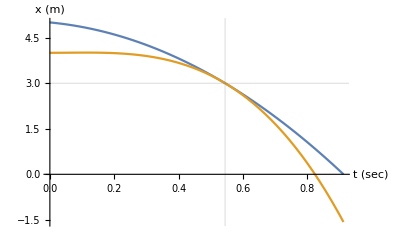
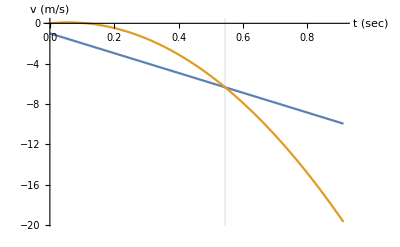
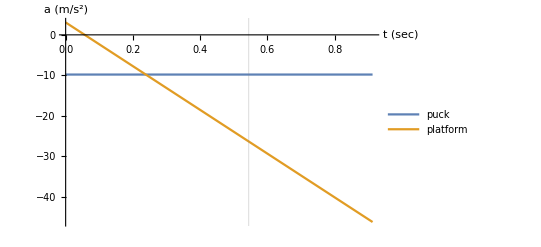
-Graphics- | -Graphics- | -Graphics-

```mathematica
T = x1[t] //. physicsRules /. conRules // Solve[{#==0,t>0},t]&//ReplaceAll[t, #]& // First;
p1={x1[t],x2[t]} // 
ReplaceRepeated[#,physicsRules]& //
	ReplaceRepeated[#,a2sol]& //
			ReplaceRepeated[#,tsolx]& //
		ReplaceRepeated[#,conRules]& //
			Plot[#,{t,0,T},
			GridLines->({{tcatch},{xcatch}}/.tsolx/.conRules),
			AxesLabel->{"t (sec)","x (m)"}
			]&;
p2={v1[t],v2[t]} // 
ReplaceRepeated[#,physicsRules]& //
	ReplaceRepeated[#,a2sol]& //
			ReplaceRepeated[#,tsolx]& //
		ReplaceRepeated[#,conRules]& //
			Plot[#,{t,0,T},
			GridLines->({{tcatch},{}}/.tsolx/.conRules),
			AxesLabel->{"t (sec)","v (m/s)"}
			]&;
p3={a1[t],a2[t]} // 
ReplaceRepeated[#,physicsRules]& //
	ReplaceRepeated[#,a2sol]& //
			ReplaceRepeated[#,tsolx]& //
		ReplaceRepeated[#,conRules]& //
			Plot[#,{t,0,T},
			GridLines->({{tcatch},{}}/.tsolx/.conRules),
			AxesLabel->{"t (sec)","a (m/s^2)"},
			PlotLegends->{"puck","platform"}
			]&;
{{p1,p2,p3}} // Grid[#,Frame->True,FrameStyle->Gray]&
```

## Deceleration

After the catch, let’s fit a linear deceleration curve to match two more conditions:
(1) the position is xf at tf and (2) the velocity is zero at tf.

```mathematica
con3 = x1p[t] == xf // 
ReplaceRepeated[#,physicsRules]& //
	ReplaceRepeated[#,t->tf]& //
		Simplify[#,Assumptions->0<tcatch<tf]&;
con4 = v1p[t] == 0 //
ReplaceRepeated[#,physicsRules]& //
	ReplaceRepeated[#,t->tf]&//
		Simplify[#,Assumptions->0<tcatch<tf]&;
```

```mathematica
a2psol = {con3,con4} // Solve[#,{bd0,sd0},Reals]& // 
Simplify[#,Assumptions->{0<tcatch<tf}]&;
```

Now take a look at the acceleration piecewise, before and after the catch.

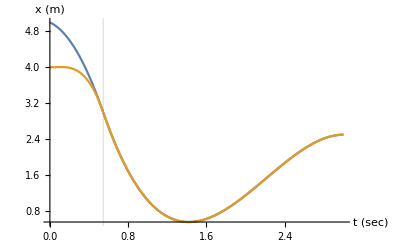
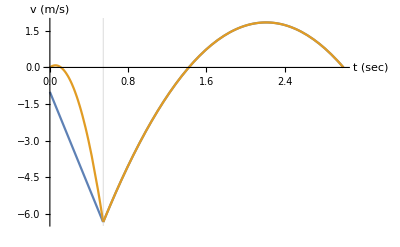
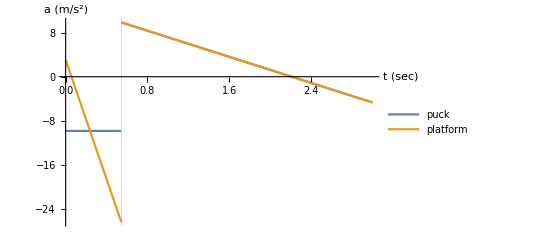
-Graphics- | -Graphics- | -Graphics-

```mathematica
T = tf /. conRules;
p1={x1p[t],x2p[t]} // 
ReplaceRepeated[#,physicsRules]& //
	ReplaceRepeated[#,a2sol]& //
		ReplaceRepeated[#,a2psol]& //
			ReplaceRepeated[#,tsolx]& //
				ReplaceRepeated[#,conRules]& //
					Plot[#,{t,0,T},
					GridLines->({{tcatch},{}}/.tsolx/.conRules),
					AxesLabel->{"t (sec)","x (m)"}
					]&;
p2={v1p[t],v2p[t]} // 
ReplaceRepeated[#,physicsRules]& //
	ReplaceRepeated[#,a2sol]& //
		ReplaceRepeated[#,a2psol]& //
			ReplaceRepeated[#,tsolx]& //
				ReplaceRepeated[#,conRules]& //
					Plot[#,{t,0,T},
					GridLines->({{tcatch},{}}/.tsolx/.conRules),
					AxesLabel->{"t (sec)","v (m/s)"}
					]&;
p3={a1p[t],a2p[t]} // 
ReplaceRepeated[#,physicsRules]& //
	ReplaceRepeated[#,a2sol]& //
		ReplaceRepeated[#,a2psol]& //
			ReplaceRepeated[#,tsolx]& //
				ReplaceRepeated[#,conRules]& //
					Plot[#,{t,0,T},
					GridLines->({{tcatch},{}}/.tsolx/.conRules),
					AxesLabel->{"t (sec)","a (m/s^2)"},
					PlotLegends->{"puck","platform"},
					PlotRange->All
				]&;
{{p1,p2,p3}} // Grid[#,Frame->True,FrameStyle->Gray]&
```

## Export to Matlab

Load the ToMatlab package. 
Download it here: http://library.wolfram.com/infocenter/MathSource/577/.
Install it using File > Install ... > Package, then browse for the file you downloaded.
Load it with the following command.

```mathematica
<<ToMatlab`
```

Export the piecewise position expressions.

```mathematica
myMatlabPrint[des_,exp_]:=Print[des,":\n",exp];
```

```mathematica
dum=x2p[t]//Simplify[#,Assumptions->{0<t≤tf,tcatch>0}]& ;
Simplify[dum,Assumptions->{t==0,tcatch>0}]//
ToMatlab//myMatlabPrint["for t==0",#]&
Simplify[dum,Assumptions->t<tcatch]//
ToMatlab//myMatlabPrint["for t<tcatch",#]&
Simplify[dum,Assumptions->t==tcatch]//
ToMatlab//myMatlabPrint["for t==tcatch",#]&
Simplify[dum,Assumptions->t>tcatch]//
ToMatlab//myMatlabPrint["for t>tcatch",#]&
```

for t==0:
x20;

for t<tcatch:
(1/6).*t.*(3.*b20.*t+s20.*t.^2+6.*v20)+x20;

for t==tcatch:
(1/6).*tcatch.*(3.*b20.*tcatch+s20.*tcatch.^2+6.*v20)+x20;

for t>tcatch:
(1/6).*(3.*bd0.*(t+(-1).*tcatch).^2+6.*b20.*t.*tcatch+(-3).*b20.* ...
  tcatch.^2+3.*s20.*t.*tcatch.^2+(-2).*s20.*tcatch.^3+sd0.*(t+(-1).* ...
  tcatch).^2.*(t+2.*tcatch)+6.*t.*v20)+x20;

The position can be differentiated to get velocity and acceleration, if needed (or we can print them like this).
We should also print the solutions for the parameters required.

```mathematica
b20/.a2sol//First//ToMatlab//myMatlabPrint["b20",#]&
s20/.a2sol//First//ToMatlab//myMatlabPrint["s20",#]&
bd0/.a2psol//First//ToMatlab//myMatlabPrint["bd0",#]&
sd0/.a2psol//First//ToMatlab//myMatlabPrint["sd0",#]&
tcatch/.tsolx//ToMatlab//myMatlabPrint["tcatch",#]&
```

b20:
(-1).*g.*(v10.^2+g.*((-1).*x10+xcatch)+v10.*(v10.^2+2.*g.*((-1).* ...
  x10+xcatch)).^(1/2)).^(-2).*(2.*v10.^4+2.*v10.^3.*((-2).*v20+( ...
  v10.^2+(-2).*g.*x10+2.*g.*xcatch).^(1/2))+v10.^2.*(g.*((-5).*x10+ ...
  3.*x20+2.*xcatch)+(-4).*v20.*(v10.^2+(-2).*g.*x10+2.*g.*xcatch).^( ...
  1/2))+g.*(x10+(-1).*xcatch).*(g.*(2.*x10+(-3).*x20+xcatch)+2.* ...
  v20.*(v10.^2+(-2).*g.*x10+2.*g.*xcatch).^(1/2))+3.*g.*v10.*(2.* ...
  v20.*(x10+(-1).*xcatch)+((-1).*x10+x20).*(v10.^2+(-2).*g.*x10+2.* ...
  g.*xcatch).^(1/2)));

s20:
3.*g.^2.*(v10+(v10.^2+2.*g.*((-1).*x10+xcatch)).^(1/2)).^(-1).*( ...
  v10.^2+g.*((-1).*x10+xcatch)+v10.*(v10.^2+2.*g.*((-1).*x10+xcatch) ...
  ).^(1/2)).^(-1).*((-1).*v10.^2+2.*g.*(x10+(-1).*x20)+v20.*(v10.^2+ ...
  (-2).*g.*x10+2.*g.*xcatch).^(1/2)+v10.*(v20+(-1).*(v10.^2+(-2).* ...
  g.*x10+2.*g.*xcatch).^(1/2)));

bd0:
(tcatch+(-1).*tf).^(-3).*(g.*tcatch.*(tcatch.^2+tcatch.*tf+4.* ...
  tf.^2)+4.*tcatch.^2.*v10+tcatch.*(4.*tf.*v10+6.*x10+(-6).*xf)+2.* ...
  tf.*(2.*tf.*v10+3.*x10+(-3).*xf));

sd0:
(-6).*(tcatch+(-1).*tf).^(-3).*(g.*tcatch.*tf+tcatch.*v10+tf.*v10+ ...
  2.*x10+(-2).*xf);

tcatch:
g.^(-1).*((-1).*v10+(-1).*(v10.^2+(-2).*g.*x10+2.*g.*xcatch).^( ...
  1/2));